## Yukawa potential analysis

### Yukawa potential definition. Solve [-(∂^2+2/r ∂) /2μ - L(L+1)/2μ r^2 + U(r)/2μ ] ψ = k^2/2μ ψ ψ = u/r -> [-∂_r^2 + L(L+1)/r^2 + U(r) ] u = k^2 u

```mathematica
LaunchKernels[10]
ParallelEvaluate[$RecursionLimit=5500];
```

{Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10)}

#### Solve for the regular solution near the origin for U(r) = -g/r E^(-r)

```mathematica
Clear[U,g]
U[g_,r_] = - g/r E^(-r);
```

```mathematica
Ueff[L_,g_,r_]=U[g,r]+L(L+1)/r^2;
```

#### resonances might be expected for L=1, g=6 or L=2, g=20.

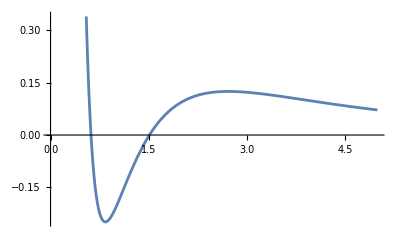

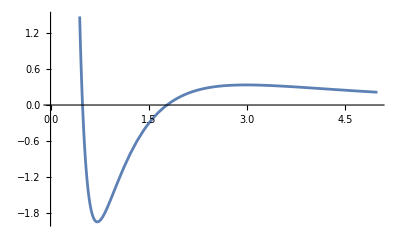

^6

```mathematica
Plot[Ueff[1,6,r],{r,0,5}]
Plot[Ueff[2,20,r],{r,0,5}]
```

### Solve the Schrodinger equation

```mathematica
Clear[u0,cc,eq,uinit,Duinit]
u0[L_,r_] =r^L( r + Sum[cc[n] r^n/n! ,{n,2,10}]);
eq[L_,r_,g_]=FullSimplify[Series[r^(-L)(-D[u0[L,r],{r,2}] + L(L+1)/r^2 u0[L,r] +U[g,r]u0[L,r] - k^2 u0[L,r]),{r,0,8}]];
```

```mathematica
eq[L,r,g]
```

(-g-(1+L) cc[2])+(g-k^2-1/2 g cc[2]-1/3 (3+2 L) cc[3]) r+1/12 (6 g cc[2]-6 k^2 cc[2]-2 g (3+cc[3])-3 (2+L) cc[4]) r^2+1/120 (-5 g (-4+6 cc[2]-4 cc[3]+cc[4])-4 (5 k^2 cc[3]+(5+2 L) cc[5])) r^3+1/360 (-15 k^2 cc[4]+15 g (-1+2 cc[2]-2 cc[3]+cc[4])-3 g cc[5]-5 (3+L) cc[6]) r^4+((-7 g (-6+15 cc[2]-20 cc[3]+15 cc[4]-6 cc[5]+cc[6])-6 (7 k^2 cc[5]+(7+2 L) cc[7])) r^5)/5040+((-28 k^2 cc[6]+28 g (-1+3 cc[2]-5 cc[3]+5 cc[4]-3 cc[5]+cc[6])-4 g cc[7]-7 (4+L) cc[8]) r^6)/20160+((-9 g (-8+28 cc[2]-56 cc[3]+70 cc[4]-56 cc[5]+28 cc[6]-8 cc[7]+cc[8])-8 (9 k^2 cc[7]+(9+2 L) cc[9])) r^7)/362880+((-45 k^2 cc[8]+5 g (-9+36 cc[2]-84 cc[3]+126 cc[4]-126 cc[5]+84 cc[6]-36 cc[7]+9 cc[8]-cc[9])-9 (5+L) cc[10]) r^8)/1814400+O[r]^9

```mathematica
Clear[ccsol];
ccsol[k_,g_]=FullSimplify[Solve[Table[SeriesCoefficient[eq[L,r,g],n]==0,{n,0,8}],Table[cc[n],{n,2,10}]],Assumptions->{L>=0, L∈Integers}][[1]]
```

{cc[2]→-g/(1+L),cc[3]→(3 g^2)/(2 (1+L))-(3 ((-1+g) g+k^2))/(3+2 L),cc[4]→-(g (g^2+2 (1+L) (3+2 L)-2 k^2 (4+3 L)+g (8+6 L)))/((1+L) (2+L) (3+2 L)),cc[5]→(5 (g^4+12 k^4 (1+L) (2+L)-4 g (-3+6 k^2-2 L) (1+L) (2+L)+4 g^3 (5+3 L)+g^2 (66-4 k^2 (5+3 L)+4 L (22+7 L))))/(4 (1+L) (2+L) (3+2 L) (5+2 L)),cc[6]→1/(4 (1+L) (2+L) (3+L) (3+2 L) (5+2 L))3 g (-g^4-20 g^3 (2+L)-4 (1+L) (2+L) (3+2 L) (5+2 L)+8 k^2 (1+L) (5+2 L) (9+5 L)-4 k^4 (46+5 L (11+3 L))+2 g^2 (-173+10 k^2 (2+L)-10 L (19+5 L))+4 g (-156+2 k^2 (46+5 L (11+3 L))-L (283+L (163+30 L)))),cc[7]→1/(8 (1+L) (2+L) (3+L) (3+2 L) (5+2 L) (7+2 L))7 (g^6-120 k^6 (1+L) (2+L) (3+L)+10 g^5 (7+3 L)+8 g (1+L) (2+L) (3+L) (45 k^4+(3+2 L) (5+2 L)-5 k^2 (13+6 L))+2 g^4 (623-5 k^2 (7+3 L)+10 L (58+13 L))+4 g^3 (1551-2 k^2 (196+15 L (13+3 L))+L (2368+L (1153+180 L)))+4 g^2 (k^4 (196+15 L (13+3 L))-k^2 (1545+L (2551+2 L (653+105 L)))+2 (855+L (1901+L (1508+L (509+62 L)))))),cc[8]→(g (-g^6-14 g^5 (8+3 L)+14 g^4 (-254+k^2 (8+3 L)-5 L (41+8 L))+4 g^3 (-9384+14 k^2 (88+15 L (5+L))-7 L (1758+L (739+100 L)))+8 (-((1+L) (2+L) (3+L) (3+2 L) (5+2 L) (7+2 L))+3 k^2 (1+L) (2+L) (5+2 L) (7+2 L) (18+7 L)-3 k^4 (1+L) (7+2 L) (180+7 L (23+5 L))+3 k^6 (352+7 L (76+5 L (7+L))))-4 g^2 (30207+7 k^4 (88+15 L (5+L))+L (57500+L (39223+28 L (408+43 L)))-k^2 (12192+7 L (2449+2 L (539+75 L))))-24 g (3600+3 k^4 (352+7 L (76+5 L (7+L)))+L (9283+L (9106+L (4273+964 L+84 L^2)))-k^2 (4512+L (9150+L (6511+21 L (93+10 L)))))))/(2 (1+L) (2+L) (3+L) (4+L) (3+2 L) (5+2 L) (7+2 L)),cc[9]→(9 (g^8+56 g^7 (3+L)+1680 k^8 (1+L) (2+L) (3+L) (4+L)-16 g (1+L) (2+L) (3+L) (4+L) (420 k^6+56 k^2 (3+L) (5+2 L)-(3+2 L) (5+2 L) (7+2 L)-70 k^4 (17+6 L))-28 g^6 (-309+2 k^2 (3+L)-2 L (110+19 L))-8 g^5 (-20764+14 k^2 (114+5 L (17+3 L))-7 L (3403+3 L (419+50 L)))+4 g^4 (14 k^4 (114+5 L (17+3 L))-4 k^2 (15837+7 L (2759+2 L (531+65 L)))+3 (97429+4 L (40256+L (23967+7 L (874+81 L)))))+32 g^3 (80967+3 k^4 (1636+7 L (301+15 L (8+L)))-k^2 (45930+L (80926+L (50413+63 L (211+20 L))))+L (181355+L (155149+L (63704+3 L (4203+322 L)))))-16 g^2 (-77805+2 k^6 (1636+7 L (301+15 L (8+L)))-k^4 (44604+L (84407+L (55357+14 L (1081+105 L))))-L (224916+L (257665+L (150594+L (47587+7740 L+508 L^2))))+2 k^2 (63945+2 L (75182+L (66361+L (27844+L (5599+434 L))))))))/(16 (1+L) (2+L) (3+L) (4+L) (3+2 L) (5+2 L) (7+2 L) (9+2 L)),cc[10]→(5 g (-g^8-24 g^7 (10+3 L)+12 g^6 (k^2 (20+6 L)-7 (223+2 L (71+11 L)))+8 g^5 (-73936+42 k^2 (86+57 L+9 L^2)-21 L (3587+L (1181+126 L)))-12 g^4 (643693+14 k^4 (86+57 L+9 L^2)-4 k^2 (20945+7 L (3217+L (1099+120 L)))+2 L (468871+L (247189+14 L (4006+331 L))))+16 (-((1+L) (2+L) (3+L) (4+L) (3+2 L) (5+2 L) (7+2 L) (9+2 L))+4 k^2 (1+L) (2+L) (3+L) (5+2 L) (7+2 L) (9+2 L) (31+9 L)-18 k^4 (1+L) (2+L) (7+2 L) (9+2 L) (200+3 L (43+7 L))+36 k^6 (1+L) (9+2 L) (700+L (799+7 L (42+5 L)))-9 k^8 (4504+L (7906+7 L (681+5 L (34+3 L)))))-96 g^3 (402538+k^4 (7180+63 L (128+5 L (9+L)))-k^2 (124726+L (192809+L (106150+7 L (3551+300 L))))+L (790083+L (595367+L (216228+5 L (7597+518 L)))))+16 g^2 (-3831561+2 k^6 (7180+63 L (128+5 L (9+L)))-3 k^4 (158964+L (261463+L (150673+42 L (868+75 L))))-L (9744939+L (9855792+L (5100286+L (1430517+20 L (10347+605 L)))))+6 k^2 (475224+L (987024+L (774496+L (289853+4 L (13021+903 L))))))+16 g (-1265040+36 k^6 (4504+L (7906+7 L (681+5 L (34+3 L))))-6 k^4 (208112+L (459092+L (376317+L (145462+315 L (85+6 L)))))+12 k^2 (219300+L (577645+L (596192+L (312439+14 L (6313+L (919+54 L))))))-L (4007118+L (5176145+L (3553812+L (1407071+2 L (161265+2 L (9941+510 L)))))))))/(16 (1+L) (2+L) (3+L) (4+L) (5+L) (3+2 L) (5+2 L) (7+2 L) (9+2 L))}

#### initialization data

```mathematica
Clear[ccsol]
ccsol[k_,g_,L_]={cc[2]->-g/(1+L),cc[3]->(3 g^2)/(2 (1+L))-(3 ((-1+g) g+k^2))/(3+2 L),cc[4]->-(g (g^2+2 (1+L) (3+2 L)-2 k^2 (4+3 L)+g (8+6 L)))/((1+L) (2+L) (3+2 L)),cc[5]->(5 (g^4+12 k^4 (1+L) (2+L)-4 g (-3+6 k^2-2 L) (1+L) (2+L)+4 g^3 (5+3 L)+g^2 (66-4 k^2 (5+3 L)+4 L (22+7 L))))/(4 (1+L) (2+L) (3+2 L) (5+2 L)),cc[6]->(3 g (-g^4-20 g^3 (2+L)-4 (1+L) (2+L) (3+2 L) (5+2 L)+8 k^2 (1+L) (5+2 L) (9+5 L)-4 k^4 (46+5 L (11+3 L))+2 g^2 (-173+10 k^2 (2+L)-10 L (19+5 L))+4 g (-156+2 k^2 (46+5 L (11+3 L))-L (283+L (163+30 L)))))/(4 (1+L) (2+L) (3+L) (3+2 L) (5+2 L)),cc[7]->(7 (g^6-120 k^6 (1+L) (2+L) (3+L)+10 g^5 (7+3 L)+8 g (1+L) (2+L) (3+L) (45 k^4+(3+2 L) (5+2 L)-5 k^2 (13+6 L))+2 g^4 (623-5 k^2 (7+3 L)+10 L (58+13 L))+4 g^3 (1551-2 k^2 (196+15 L (13+3 L))+L (2368+L (1153+180 L)))+4 g^2 (k^4 (196+15 L (13+3 L))-k^2 (1545+L (2551+2 L (653+105 L)))+2 (855+L (1901+L (1508+L (509+62 L)))))))/(8 (1+L) (2+L) (3+L) (3+2 L) (5+2 L) (7+2 L)),cc[8]->(g (-g^6-14 g^5 (8+3 L)+14 g^4 (-254+k^2 (8+3 L)-5 L (41+8 L))+4 g^3 (-9384+14 k^2 (88+15 L (5+L))-7 L (1758+L (739+100 L)))+8 (-((1+L) (2+L) (3+L) (3+2 L) (5+2 L) (7+2 L))+3 k^2 (1+L) (2+L) (5+2 L) (7+2 L) (18+7 L)-3 k^4 (1+L) (7+2 L) (180+7 L (23+5 L))+3 k^6 (352+7 L (76+5 L (7+L))))-4 g^2 (30207+7 k^4 (88+15 L (5+L))+L (57500+L (39223+28 L (408+43 L)))-k^2 (12192+7 L (2449+2 L (539+75 L))))-24 g (3600+3 k^4 (352+7 L (76+5 L (7+L)))+L (9283+L (9106+L (4273+964 L+84 L^2)))-k^2 (4512+L (9150+L (6511+21 L (93+10 L)))))))/(2 (1+L) (2+L) (3+L) (4+L) (3+2 L) (5+2 L) (7+2 L)),cc[9]->(9 (g^8+56 g^7 (3+L)+1680 k^8 (1+L) (2+L) (3+L) (4+L)-16 g (1+L) (2+L) (3+L) (4+L) (420 k^6+56 k^2 (3+L) (5+2 L)-(3+2 L) (5+2 L) (7+2 L)-70 k^4 (17+6 L))-28 g^6 (-309+2 k^2 (3+L)-2 L (110+19 L))-8 g^5 (-20764+14 k^2 (114+5 L (17+3 L))-7 L (3403+3 L (419+50 L)))+4 g^4 (14 k^4 (114+5 L (17+3 L))-4 k^2 (15837+7 L (2759+2 L (531+65 L)))+3 (97429+4 L (40256+L (23967+7 L (874+81 L)))))+32 g^3 (80967+3 k^4 (1636+7 L (301+15 L (8+L)))-k^2 (45930+L (80926+L (50413+63 L (211+20 L))))+L (181355+L (155149+L (63704+3 L (4203+322 L)))))-16 g^2 (-77805+2 k^6 (1636+7 L (301+15 L (8+L)))-k^4 (44604+L (84407+L (55357+14 L (1081+105 L))))-L (224916+L (257665+L (150594+L (47587+7740 L+508 L^2))))+2 k^2 (63945+2 L (75182+L (66361+L (27844+L (5599+434 L))))))))/(16 (1+L) (2+L) (3+L) (4+L) (3+2 L) (5+2 L) (7+2 L) (9+2 L)),cc[10]->(5 g (-g^8-24 g^7 (10+3 L)+12 g^6 (k^2 (20+6 L)-7 (223+2 L (71+11 L)))+8 g^5 (-73936+42 k^2 (86+57 L+9 L^2)-21 L (3587+L (1181+126 L)))-12 g^4 (643693+14 k^4 (86+57 L+9 L^2)-4 k^2 (20945+7 L (3217+L (1099+120 L)))+2 L (468871+L (247189+14 L (4006+331 L))))+16 (-((1+L) (2+L) (3+L) (4+L) (3+2 L) (5+2 L) (7+2 L) (9+2 L))+4 k^2 (1+L) (2+L) (3+L) (5+2 L) (7+2 L) (9+2 L) (31+9 L)-18 k^4 (1+L) (2+L) (7+2 L) (9+2 L) (200+3 L (43+7 L))+36 k^6 (1+L) (9+2 L) (700+L (799+7 L (42+5 L)))-9 k^8 (4504+L (7906+7 L (681+5 L (34+3 L)))))-96 g^3 (402538+k^4 (7180+63 L (128+5 L (9+L)))-k^2 (124726+L (192809+L (106150+7 L (3551+300 L))))+L (790083+L (595367+L (216228+5 L (7597+518 L)))))+16 g^2 (-3831561+2 k^6 (7180+63 L (128+5 L (9+L)))-3 k^4 (158964+L (261463+L (150673+42 L (868+75 L))))-L (9744939+L (9855792+L (5100286+L (1430517+20 L (10347+605 L)))))+6 k^2 (475224+L (987024+L (774496+L (289853+4 L (13021+903 L))))))+16 g (-1265040+36 k^6 (4504+L (7906+7 L (681+5 L (34+3 L))))-6 k^4 (208112+L (459092+L (376317+L (145462+315 L (85+6 L)))))+12 k^2 (219300+L (577645+L (596192+L (312439+14 L (6313+L (919+54 L))))))-L (4007118+L (5176145+L (3553812+L (1407071+2 L (161265+2 L (9941+510 L)))))))))/(16 (1+L) (2+L) (3+L) (4+L) (5+L) (3+2 L) (5+2 L) (7+2 L) (9+2 L))};
```

```mathematica
Clear[uinit,Duinit];
uinit[L_,r_,k_,g_] = u0[L,r]/.ccsol[k,g,L];
Duinit[L_,r_,k_,g_] = D[u0[L,r],r]/.ccsol[k,g,L];
```

#### Solve the differential equation, initializing at r0=1/100, out to rf = 20.

```mathematica
Clear[x,y,solution]
r0= 1/1000;
rf=30;solution[L_,k_,g_]:=NDSolve[{-y'[r] + (L(L+1)/r^2+U[g,r]-k^2) x[r]==0,y[r]==x'[r],x[r0] ==uinit[L,r0,k,g],y[r0] == Duinit[L,r0,k,g]},{x,y},{r,r0,rf}  ][[1]]
```

#### project out the incoming and outgoing plane wave components

```mathematica
Clear[outwave]
pcd[L_,k_,g_]:=(uout = Evaluate[x[rf]/.solution[L,k,g]];duout = Evaluate[y[rf]/.solution[L,k,g]];JYcoeffs={SphericalBesselY[L,k rf](k uout (L+1)- k rf duout)-SphericalBesselY[1+L,k rf](k^2 rf uout),-(SphericalBesselJ[L,k rf](k uout (L+1)- k rf duout)-SphericalBesselJ[1+L,k rf](k^2 rf uout))};-k^(2L+1) JYcoeffs[[1]]/JYcoeffs[[2]])
```

```mathematica
outwave[1,.1,2]
```

outwave[1,0.1,2]

```mathematica
pcdtable[L_,g_]:=Chop[ParallelTable[{k,pcd[L,k,g]},{k,0.00001,3,.001}]];
deltatable[L_,g_]:={#[[1]],ArcCot[#[[2]]/((#[[1]])^(2l+1))]}&/@pcdtable[L,g];
```

## Plots of p^(2L+1) Cot[δ] for different L and g

### L=0

#### g=0.1, g=0.5, g=1, g=2, g=6

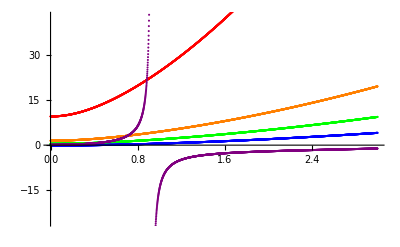

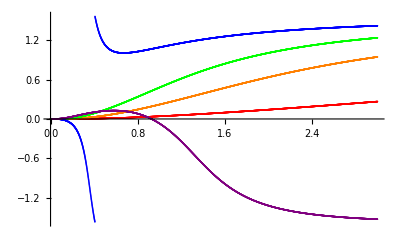

```mathematica
L0=0;ListPlot[{pcdtable[L0,.1],pcdtable[L0,.5],pcdtable[L0,1],pcdtable[L0,2],pcdtable[L0,6]},PlotStyle->{Red,Orange,Green,Blue,Purple}]
ListPlot[{deltatable[L0,.1],deltatable[L0,.5],deltatable[L0,1],deltatable[L0,2],deltatable[L0,6]},PlotStyle->{Red,Orange,Green,Blue,Purple}]
```

### L=1

#### g=0.1, g=0.5, g=1, g=2, g=6, g=10

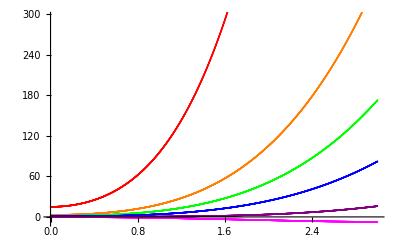

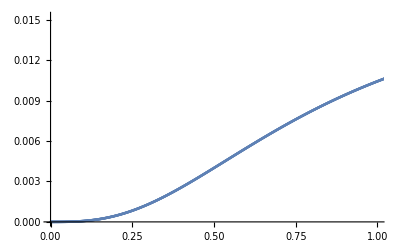

```mathematica
L0=1;ListPlot[{pcdtable[L0,.1],pcdtable[L0,.5],pcdtable[L0,1],pcdtable[L0,2],pcdtable[L0,6],pcdtable[L0,10]},PlotStyle->{Red,Orange,Green,Blue,Purple,Magenta}]
ListPlot[deltatable[L0,.1],PlotRange->{{0,1},All}]
```

### L=2

#### g=0.1, g=0.5, g=1, g=2, g=6, g=20

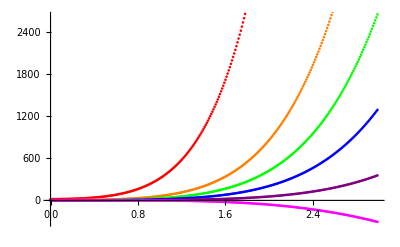

```mathematica
L0=2;ListPlot[{pcdtable[L0,.1],pcdtable[L0,.5],pcdtable[L0,1],pcdtable[L0,2],pcdtable[L0,6],pcdtable[L0,20]},PlotStyle->{Red,Orange,Green,Blue,Purple,Magenta}]
```

### L=5

#### g=0.1, g=1, g=5, g=10, g=50, g=100

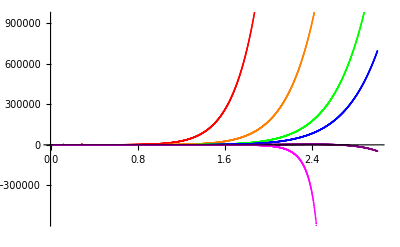

```mathematica
L0=5;ListPlot[{pcdtable[L0,.1],pcdtable[L0,1],pcdtable[L0,5],pcdtable[L0,10],pcdtable[L0,50],pcdtable[L0,100]},PlotStyle->{Red,Orange,Green,Blue,Purple,Magenta}]
```